```mathematica
Clear["Global`*"]
```

#### Stationary optimization

Loading the package

```mathematica
Needs["NDSolve`FEM`"]
```

Defining the system of equation

```mathematica
Clear[u,v,x,y]
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

Defining the geometric region

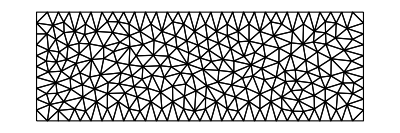

```mathematica
a=1.0;
reg1=Rectangle[{0,0},{30,10}];
(*reg2=Rectangle[{0,20},{5,40}];
reg3=Rectangle[{15,20},{20,40}];
reg4=Rectangle[{5,35},{15,40}];*)
(*Ω=RegionUnion[reg1,reg2,reg3,reg4];*)
mesh=ToElementMesh[reg1,"MaxCellMeasure"->1,"MeshOrder"->2,"MeshElementType"->TriangleElement];
mesh["Wireframe"]
```

Defining boundary conditions

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0,x==0];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0,x==0];
Subscript[Γ, Nv]=NeumannValue[-1,x==30&&3<y<7];
```

Replacing the Young modulus and Poisson ratio in system of equations

```mathematica
op1=op/.{Y->10^3,ν->33/100};
```

Computations

```mathematica
{state}=NDSolve`ProcessEquations[{op1=={0,Subscript[Γ, Nv]},Subscript[Γ, Du],Subscript[Γ, Dv]},{u,v},{x,y}∈mesh]
femdata=state["FiniteElementData"];
pded=femdata["PDECoefficientData"];
bcd=femdata["BoundaryConditionData"];
md=femdata["FEMMethodData"];
sd=state["SolutionData"][[1]];
vd=state["VariableData"];
discretePDE=DiscretizePDE[pded,md,sd]
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
discreteBCs=DiscretizeBoundaryConditions[bcd,md,sd]
ele=DiscretizePDE[pded,md,sd,"SaveFiniteElements"->True]
{stiffnessElements,nonzeroPos}=ele["StiffnessElements"];
```

{NDSolve`StateData[<SteadyState>]}

DiscretizedPDEData[<2050>]

DiscretizedBoundaryConditionData[<2050>]

DiscretizedPDEData[<2050>]

Defining the densities and modified stiffness matrix

```mathematica
density=Table[ρ[i],{i,1,Length@stiffnessElements}];
modifiedElements=(density^2)*stiffnessElements;
Length@stiffnessElements
```

472

Assemble

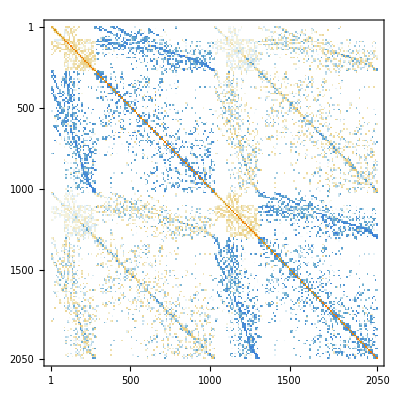
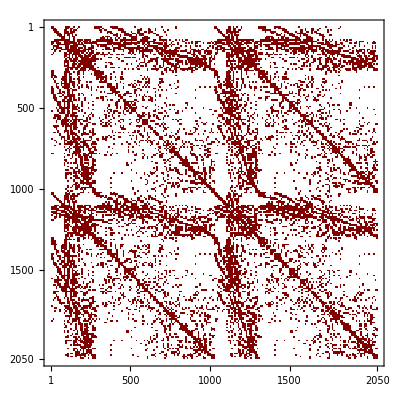

```mathematica
dof=md["DegreesOfFreedom"];
inci=Join@@md["Incidents"];
modifiedstiffness=AssembleMatrix[{inci,inci},modifiedElements,{dof,dof},"Sparse"->nonzeroPos];
{MatrixPlot[stiffness],MatrixPlot[modifiedstiffness]}
```

Defining the unknown displacements and extracting the coords of elements from mesh

```mathematica
displacement=Table[δ[i],{i,1,Length[stiffness]}];
coords=mesh["Coordinates"];
elems=mesh["MeshElements"];
```

Deploying boundary conditions on initial matrix and modified

```mathematica
DeployBoundaryConditions[{load,stiffness},discreteBCs];
DeployBoundaryConditions[{load,modifiedstiffness},discreteBCs];
```

Flattening the load vector for goal function

```mathematica
loadF=Flatten[load];
```

Defining the “area” of finite elements

```mathematica
square=Join@@mesh["MeshElementMeasure"];
```

```mathematica
goalFunction=displacement.modifiedstiffness.displacement;
massEquation=∑_(k=1)^Length[square] square⟦k⟧ density⟦k⟧≤(∑_(k=1)^Length[square] square⟦k⟧) 0.5;
densityEq=Thread[(0≤#1≤1&)[density]];
(*densityEq=(0.9≤#1≤1||0.0≤#1≤0.1)&/@density;*)
equation=Table[modifiedstiffness⟦i⟧.displacement==loadF⟦i⟧,{i,1,Length[displacement]}];
```

```mathematica
sysOfEq=Flatten[{goalFunction,massEquation,equation,densityEq}];
sysOfEq//Length;
variables=Flatten[{density,displacement}];
variables//Length;
```

```mathematica
initDis=Thread[{#,0}&[displacement]];
initDen=Thread[{#,0.5}&[density]];
initCond=Flatten[{initDen,initDis},1];
```

```mathematica
resultFMin=Quiet[FindMinimum[sysOfEq,initCond]];//AbsoluteTiming
minimizedDen=density/.resultFMin[[2]];
```

{151.349,Null}

```mathematica
Evaluate[Table[ρ[i],{i,1,Length@stiffnessElements}]]=minimizedDen;
```

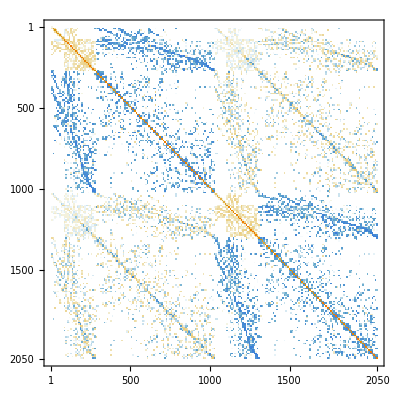
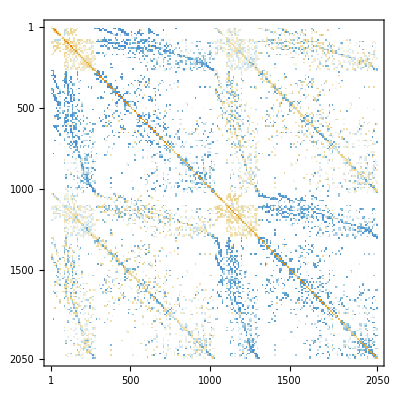

```mathematica
{MatrixPlot[stiffness],MatrixPlot[modifiedstiffness]}
```

Solving for initial matrix and modified

```mathematica
Short[solution1=LinearSolve[stiffness,load]]
Short[solution2=LinearSolve[modifiedstiffness,load]]
```

{{0.},{0.},{0.},«2045»,{-0.317508},{-0.363376}}

{{0.},{0.},{0.},«2045»,{-0.528886},{-0.595602}}

```mathematica
split=Span@@@Transpose[{Most[#+1],Rest[#]}&[md["IncidentOffsets"]]]
```

{1;;1025,1026;;2050}

```mathematica
ufun1=ElementMeshInterpolation[{mesh}, solution1[[split[[1]]]]]
vfun1=ElementMeshInterpolation[{mesh}, solution1[[split[[2]]]]]
ufun2=ElementMeshInterpolation[{mesh}, solution2[[split[[1]]]]]
vfun2=ElementMeshInterpolation[{mesh}, solution2[[split[[2]]]]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

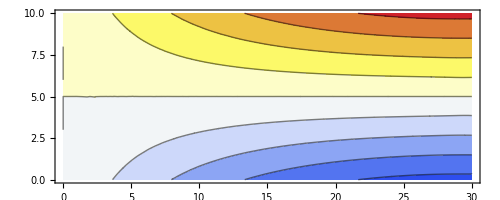
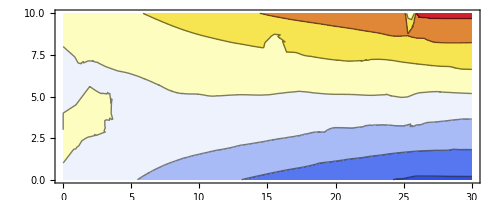

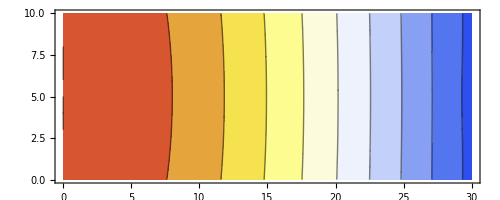
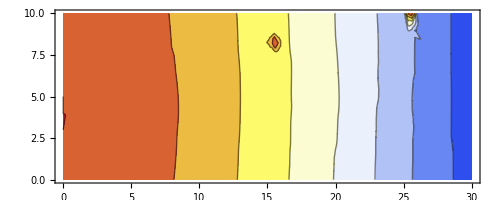

```mathematica
{ContourPlot[ufun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],ContourPlot[ufun2[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
{ContourPlot[vfun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],
ContourPlot[vfun2[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
```

```mathematica
dmesh1=ElementMeshDeformation[mesh,{ufun1,vfun1}]
dmesh2=ElementMeshDeformation[mesh,{ufun2,vfun2}]
```

ElementMesh[{{0.,30.2148},{-0.929491,10.}},{TriangleElement[<472>]}]

ElementMesh[{{0.,30.3211},{-1.48604,10.}},{TriangleElement[<472>]}]

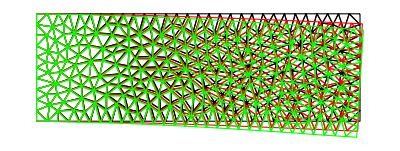

```mathematica
Show[{
mesh["Wireframe"],
dmesh1["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
dmesh2["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Green],FaceForm[]]]]
}]
```

Visualization of densities of elements

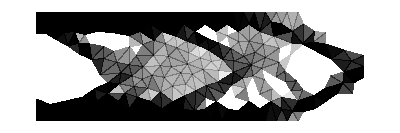

```mathematica
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]]}&]/@elems[[1,1,1;;Length[square],1;;3]]);
maxden=Max[minimizedDen];
denpolys=Transpose[{minimizedDen/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
Graphics[opacityfiltered]
```

These values are values in elements. We’d need to get the values at the nodes. Here is a way to do it. “VertexElementConnectivity” shows which  vertex is connected to which elements 1 if there is a connection and 0 is there is no connection (see documentation of ElementMesh). We then use Mean to estimate a value at a node based on the connected elements.

```mathematica
denAtNodes=Mean/@DeleteCases[Inner[Times, mesh["VertexElementConnectivity"],minimizedDen,List],0.,2.];
```

```mathematica
denIF=ElementMeshInterpolation[{mesh},denAtNodes]
```

```mathematica
ContourPlot[denIF[x,y],{x,y}∈mesh,AspectRatio->Automatic,PlotLegends->Automatic]
```

-Graphics-

#### Stress Analysis

```mathematica
ClearAll[VonMisesStress]
VonMisesStress[{ufun_InterpolatingFunction,vfun_InterpolatingFunction}, fac_]:=Block[
{dd,df,mesh,coords,dv,ux,uy,vx,vy,ex,ey,gxy,sxx,syy,sxy},
dd=Outer[(D[#1[x,y],#2])&,{ufun,vfun},{x,y}];
df=Table[Function[{x,y},Evaluate[dd[[i,j]]]],{i,2},{j,2}];
(* the coordinates from the ElementMesh *)
mesh=ufun["Coordinates"][[1]];
coords=mesh["Coordinates"];
dv =Table[df[[i,j]]@@@coords,{i,2},{j,2}];

ux=dv[[1,1]];
uy=dv[[1,2]];
vx=dv[[2,1]];
vy=dv[[2,2]];

ex=ux;
ey=vy;
gxy=(uy+vx);

sxx=fac[[1,1]]*ex+fac[[1,2]]*ey;
syy=fac[[2,1]]*ex+fac[[2,2]]*ey;
sxy=fac[[3,3]]*gxy;
ElementMeshInterpolation[{mesh},Sqrt[( sxy^2 + syy ^2+ sxx^2 )]]
]
```

```mathematica
(* fac is for plane stress *)
fac=Y/(1-ν^2)*{{1,ν,0},{ν,1,0},{0,0,(1-ν)/2}}/.{Y->10^3,ν->33/100};
vonMisesStress1 =VonMisesStress[{ufun1,vfun1},fac]
vonMisesStress2=VonMisesStress[{ufun2,vfun2},fac]
```

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

InterpolatingFunction[{{0., 5.}, {0., 2.}}, <>]

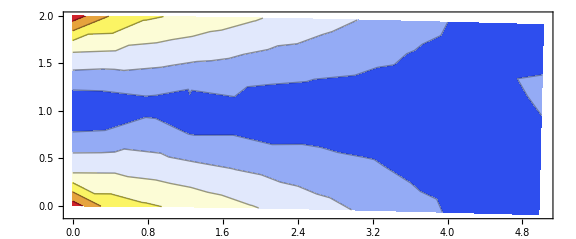

```mathematica
ElementMeshContourPlot[ vonMisesStress1["ValuesOnGrid"], ElementMeshDeformation[ufun1["ElementMesh"], {ufun1,vfun1} ],ImageSize->Large,AspectRatio->Automatic]
```

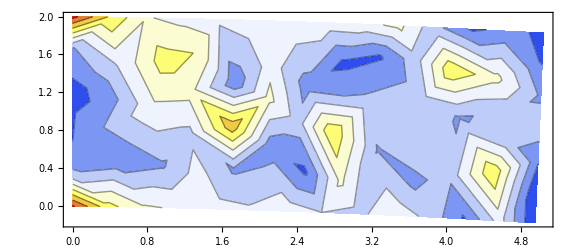

```mathematica
ElementMeshContourPlot[ vonMisesStress2["ValuesOnGrid"], ElementMeshDeformation[ufun2["ElementMesh"], {ufun2,vfun2} ],ImageSize->Large,AspectRatio->Automatic]
```

#### ...

```mathematica
{c,d}={1,2}
```

```mathematica
density=density/.resultFMin[[2]];
```

```mathematica
ρ
```

```mathematica
Evaluate[Table[ρ[i],{i,1,10}]]=Range[10]
```

```mathematica
ρ[1]
```

#### Optimization in dynamic problems

```mathematica
Clear[u,v,x,y]
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

```mathematica
a=1.0;
reg1=Rectangle[{0,0},{30,10}];
(*reg2=Rectangle[{0,20},{5,40}];
reg3=Rectangle[{15,20},{20,40}];
reg4=Rectangle[{5,35},{15,40}];*)
(*Ω=RegionUnion[reg1,reg2,reg3,reg4];*)
mesh=ToElementMesh[reg1,"MaxCellMeasure"->1,"MeshOrder"->2,"MeshElementType"->TriangleElement];
mesh["Wireframe"]
```

-Graphics-

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0,x==0];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0,x==0];
Subscript[Γ, Nv]=NeumannValue[-1,x==30&&3<y<7];
```

```mathematica
vd=NDSolve`VariableData[{"DependentVariables","Space"}->{{u,v},{x,y}}];
sd=NDSolve`SolutionData["Space"->ToNumericalRegion[mesh]];
methodData=InitializePDEMethodData[vd,sd]
```

FEMMethodData[<2050,{2,2},4>]

```mathematica
Length[mesh["Coordinates"]]*Length[NDSolve`SolutionDataComponent[vd,"DependentVariables"]]
methodData["DegreesOfFreedom"]
```

2050

2050

```mathematica
diffusionCoefficients="DiffusionCoefficients"->{{{{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}},{{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}},{{{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}},{{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}}}/.{Y->10^3,ν->33/100};
```

```mathematica
initCoeffs=InitializePDECoefficients[vd,sd,{diffusionCoefficients}];
```

```mathematica
initBCs=InitializeBoundaryConditions[vd,sd,{{Subscript[Γ, Du]},{Subscript[Γ, Dv],Subscript[Γ, Nv]}}];
```

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
```

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
split=Span@@@Transpose[{Most[#+1],Rest[#]}&[methodData["IncidentOffsets"]]];
```

```mathematica
discreteBCs=DiscretizeBoundaryConditions[initBCs,methodData,sd];
```

```mathematica
massCoefficients="MassCoefficients"->{{1,0},{0,1}}
```

```mathematica
"MassCoefficients"->{{1,0},{0,1}}
```

MassCoefficients→{{1,0},{0,1}}

```mathematica
initCoeffs=InitializePDECoefficients[vd,sd,{diffusionCoefficients,massCoefficients}]
```

PDECoefficientData[<2,2>]

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd]
```

DiscretizedPDEData[<2050>]

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

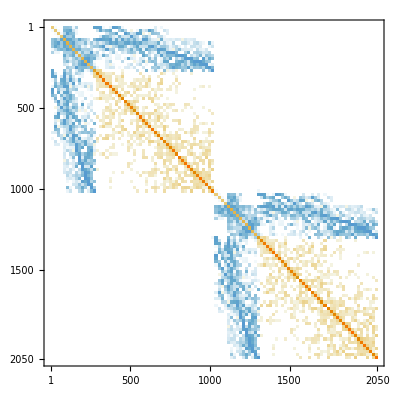

```mathematica
MatrixPlot[mass]
```

```mathematica
rayleighDamping=0.1*mass+0.04*stiffness;
```

```mathematica
DeployBoundaryConditions[{load,stiffness,rayleighDamping,mass},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

```mathematica
dof=methodData["DegreesOfFreedom"];
init=dinit=ConstantArray[0,{dof,1}];
```

```mathematica
sparsity=ArrayFlatten[{{mass["PatternArray"],mass["PatternArray"]},{rayleighDamping["PatternArray"],rayleighDamping["PatternArray"]}}]
```

SparseArray[<132132>, {4100, 4100}, Pattern]

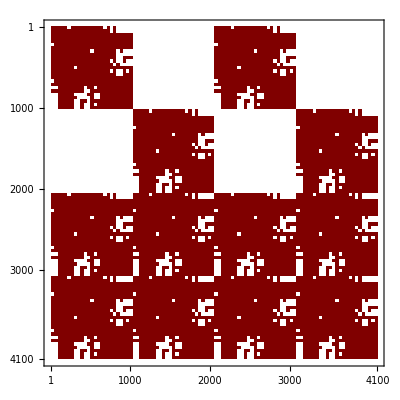

```mathematica
MatrixPlot[sparsity]
```

```mathematica
Dynamic["time: "<>ToString[CForm[currentTime]]]
AbsoluteTiming[
tfun=NDSolveValue[{
mass.u''[ t]+rayleighDamping.u'[ t]+stiffness.u[ t]==load*Sin[t*0.1]*5
,u[ 0]==init,u'[ 0]==dinit},u,{t,0,450}
,Method->{"EquationSimplification"->"Residual"}
,Jacobian->{Automatic,Sparse->sparsity}
,EvaluationMonitor:>(currentTime=t;)
]]
```

{26.6825,InterpolatingFunction[{{0., 450.}}, <>]}

```mathematica
graphics=Function[t,
dmesh=ElementMeshDeformation[mesh,Part[tfun[t],#]&/@split];
Show[{
mesh["Wireframe"["MeshElement"->"BoundaryElements"]],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]
},PlotRange->{{-1,31},{-1,11}}]]/@Range[0,450,1];
```

```mathematica
ListAnimate[graphics,SaveDefinitions->True]
```

```mathematica
energyF[t_]:=Flatten[tfun[t]].stiffness.Flatten[tfun[t]]
```

```mathematica
stiffness//Length
```

2050

```mathematica
tfun[1]//Length
```

2050

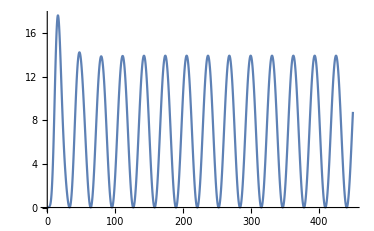

```mathematica
Plot[energyF[t],{t,0,450}]
```

#### Results